4

9

15

16

24

25

34

35

36

47

48

49

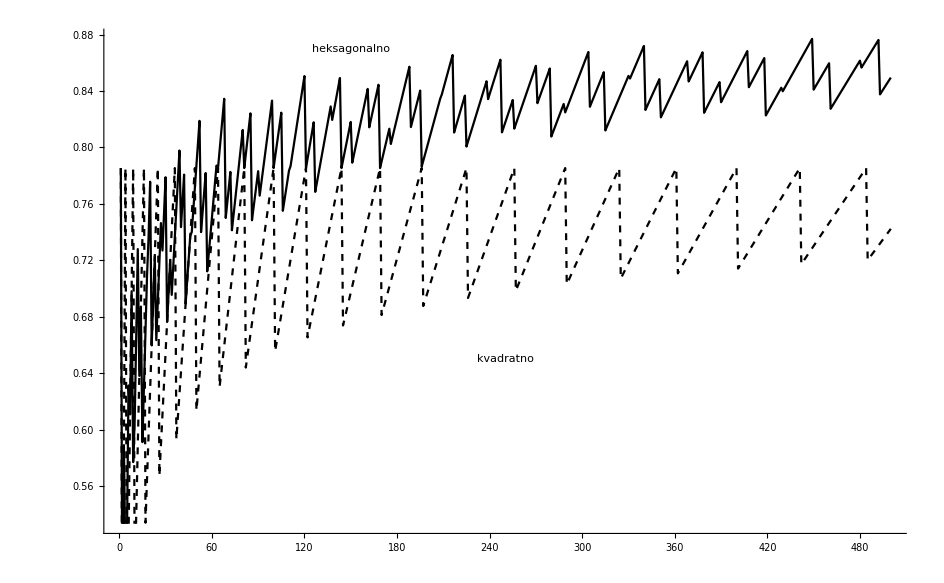

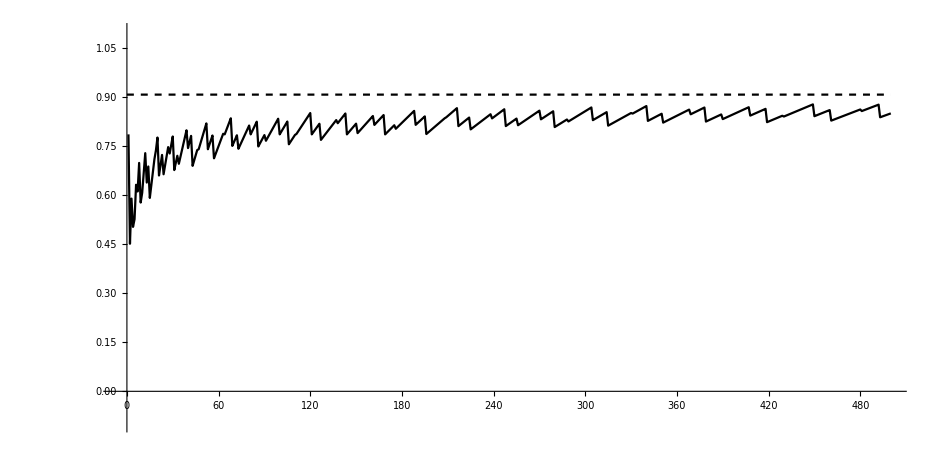

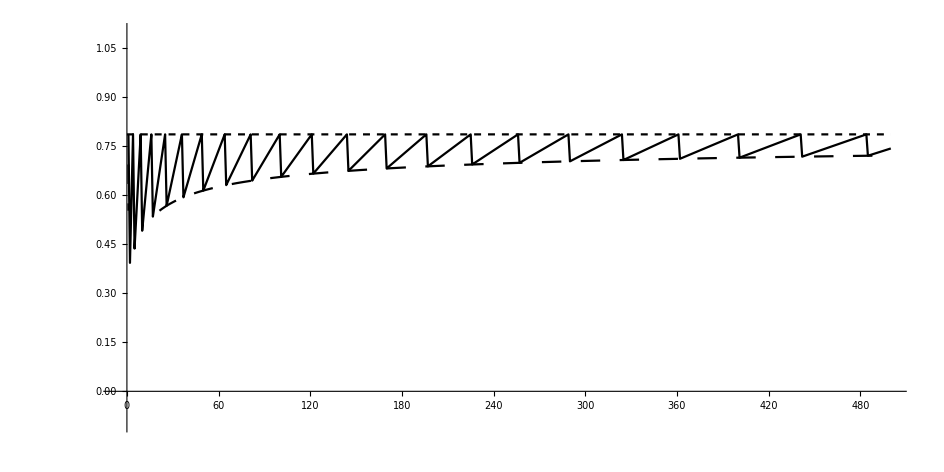

```mathematica
brojKrugova=500;

heGustoca={};
kvGustoca={};

For[unos=1,unos<brojKrugova+1,unos++,

(*%%%%%%%%%%%%%%%%   heksagonalni uzorak   %%%%%%%%%%%%%%%*)
{
l={{1,1}};
lz={{1,1}};
a={2};
b={2};
k={2};
im=1;

poma2=0;
poma={2};pomb={2};pomk={2};


For[n=2,n<unos+1,n++,
pomk1=k[[n-1]]+2;                               
For[i=1,i<im+1,i++,
{If[Mod[i,2]==1,
poma=ReplacePart[poma,i->lz[[i]][[2]]*2+2],
poma=ReplacePart[poma,i->lz[[i]][[2]]*2+3]
],
pomb=ReplacePart[pomb,i->b[[n-1]]],
pomk=ReplacePart[pomk,i->Max[poma[[i]],pomb[[i]]]],
pomk1=Min[pomk1,pomk[[i]]]
}
];
If[Mod[im,2]==1,
poma2=3,
poma2=2
];
pomb2=2+im*Sqrt[3];
pomk2=Max[poma2,pomb2];
pomk3=Min[pomk2,pomk1];
k=Join[k,{pomk3}];
If[pomk3==pomk2,
{a=Join[a,{Max[poma2,a[[n-1]]]}],
b=Join[b,{Max[pomb2,b[[n-1]]]}],
im=im+1,
l=Join[l,{{im,1}}],
lz=Join[lz,{{im,1}}],
poma=Join[poma,{poma2}],
pomb=Join[pomb,{pomb2}],
pomk=Join[pomk,{pomk2}],
},
{i=1,j=1,
While[pomk3≠pomk[[i]], j=j+1;i++],
a=Join[a,{Max[poma[[i]],a[[n-1]]]}],
b=Join[b,{pomb[[i]]}],
l=Join[l,{{i,lz[[i]][[2]]+1}}],
lz=ReplacePart[lz,i->{i,lz[[i]][[2]]+1}],
}
];
];

heG=1.*unos*Pi/k[[unos]]^2;
heGustoca=Join[heGustoca,{{unos,heG}}];



(* %%%%%%%%%%%%%%%%%%%  kvadratni uzorak  %%%%%%%%%%%%%%%%% *)

lk={};
kk=Ceiling[Sqrt[unos]];
kkkv=2*kk;

For[i=1,i<kk+1,i++,
If[i≠kk,
For[j=1,j<kk+1,j++,lk=Join[lk,{{j,i}}]],
For[j=1,j<(unos-(kk-1)*kk)+1,j++,lk=Join[lk,{{j,i}}]]
];
];

kvG=1.*unos*Pi/(kkkv^2);
kvGustoca=Join[kvGustoca,{{unos,kvG}}];
}]

For[i=1,i<unos,i++,If[kvGustoca[[i]][[2]]>heGustoca[[i]][[2]],Print[i]]];

(*  %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%   optimalno rješenje  %%%%%%%%%%%%%%%%%%%%%%%%%  
*)

opGustoca={
{1,0.785398163397448309615660845820},
{2,0.539012084452647221356168169720},
{3,0.609644808741350951447230676805},
{4,0.785398163397448309615660845820},
{5,0.673765105565809026695210212147},
{6,0.663956909464133571452413649192},
{7,0.669310826840792318436251021851},
{8,0.730963825253907837357358208947},
{9,0.785398163397448309615660845823},
{10,0.690035785264180329182022896992},
{11,0.700741577756104830198542148981},
{12,0.738468223884044498369057950509},
{13,0.733264694904101752789658211574},
{14,0.735679255542682563361972309848},
{15,0.762056010926688689309038346000},
{16,0.785398163397448309615660845820},
{17,0.733550263302331439285589240583},
{18,0.754653357875667578715912508592},
{19,0.752307896742078979509898727719},
{20,0.779493686867621861721679242594},
{21,0.753357702889674769521037881741},
{22,0.771680112098219822603167037099},
{23,0.763631032126130708837463558606},
{24,0.774963259757823779541804629695},
{25,0.785398163397448309615660845820},
{26,0.758469090483941352861819034651},
{27,0.772311456467343180199003969257},
{28,0.771854111403716173720195749792},
{29,0.778906241779735128443167917037},
{30,0.792019026460736228749276303658},
{31,0.777297478729284489847888300452},
{32,0.776004124474520585203569503088},
{33,0.788852303933884675540557918273},
{34,0.776649064332277077192193097006},
{35,0.781227212998714358933378085364},
{36,0.785398163397448309615660845814},
{37,0.783302723724208829617437864297},
{38,0.797042556834780531205882269714},
{39,0.811179027291583405559076523455},
{40,0.787979518878382871537374468078},
{41,0.792723899305009720099449735145},
{42,0.798684278653432047162866645972},
{43,0.787264166427460630119036545340},
{44,0.793842807841790391912527518373},
{45,0.789444268494961791151996201482},
{46,0.797187131992481565987478372968},
{47,0.789293882075948475945003280444},
{48,0.791144033840820484633598422519},
{49,0.791216989526925284715824261839},
{50,0.800272183997614540398268557986},
{51,0.808656948184898971918843953968},
{52,0.822530842067761468539017516644},
{53,0.814642500051039348061532079569},
{54,0.799407623083866967669545765997},
{55,0.800271297244825744992218341266},
{56,0.802351729502980578932357268915},
{57,0.803965673845865929966857781564},
{58,0.799330724318471867207813535844},
{59,0.802698827038006793401631671022},
{60,0.797139156419255784870559282609},
{61,0.801374124592793740357582679370},
{62,0.804113477816698520155376391251},
{63,0.810973780649873545826894093582},
{64,0.809685038563171020371396760575},
{65,0.815740018110047678672004161772},
{66,0.819358090828537580877710854049},
{67,0.824515655814026444371365043625},
{68,0.835021788301676498075386011080},
{69,0.816776573752215775394223611557},
{70,0.807506020669364260500664086977},
{71,0.805576954556086927019502619209},
{72,0.808908302137999085775684834734},
{73,0.808256206862671849525236295628},
{74,0.811516775123364681685174979487},
{75,0.806198017941952636005393179087},
{76,0.808699956656388340271328954084},
{77,0.809628951523275454193704449075},
{78,0.815893333309535399379288603296},
{79,0.820806922795721980813682909695},
{80,0.827217888559947854040065137731},
{81,0.823000583646207165131312975826},
{82,0.822714696667481465122043671839},
{83,0.821501474386234485434434731565},
{84,0.823339926925100792282117556322},
{85,0.827885139567273651077623069999},
{86,0.834403272414726330623353074852},
{87,0.817651999581176324044528222879},
{88,0.818344762893455338659140369860},
{89,0.813720269423130443280172100716},
{90,0.816861606107565255741672170251},
{91,0.818173810485969463957034440537},
{92,0.821619044662047529543149057267},
{93,0.818423476521143216019926914291},
{94,0.823131614711695270716775765925},
{95,0.820112788103383671049325920553},
{96,0.824168967917176961985882367615},
{97,0.827644213165413536281305095877},
{98,0.833553492453149745406906221039},
{99,0.840299937025485161853712217746},
{100,0.830030826635912821740802332440},
{101,0.827837458204886740849985234223},
{102,0.826114042027870748552195664647},
{103,0.826348041985204520696807001421},
{104,0.828249793523388576412378912418},
{105,0.832701612019226131524236043108},
{106,0.833028317748},
{107,0.823857790657640543813394281499},
{108,0.822757444973615405175483101187},
{109,0.824199710946182236760458317483},
{110,0.822274269043788233219044672300},
{111,0.825145003926722239389734741467},
{112,0.825796605618670452719327830584},
{113,0.826722100560516881572374636346},
{114,0.830935940404435353549195715333},
{115,0.829424877813220596562781585268},
{116,0.831814956318629673062000464863},
{117,0.834340904498932290987139503343},
{118,0.838960130138630368263454714313},
{119,0.845084379636190758907117056075},
{120,0.851658165016251855319555118520},
{121,0.835858472004155186816930239791},
{122,0.833256858758184480156083575988},
{123,0.830102810046943880404118740918},
{124,0.827882569489952205937044175739},
{125,0.830168776967464070098670387597},
{126,0.831372731264356975678074877441},
{127,0.831953432091018222557685985639},
{128,0.831519142296790878206793082839},
{129,0.827986391238147058571231447326},
{130,0.828611517477098202541332177922},
{131,0.829214381766750148879227621812},
{132,0.830308417787970714465006006583},
{133,0.831493735197432917683144994824},
{134,0.836041357900107352235235228899},
{135,0.837258741624934135097297719008},
{136,0.840505786196431512104286567291},
{137,0.844386136710202177869379241425},
{138,0.840559517817220290171235730530},
{139,0.843331425575420809020868982393},
{140,0.843960434882289276826864877332},
{141,0.844317892155816320237596014649},
{142,0.847121206056549661879903943045},
{143,0.851282016761247835788454445056},
{144,0.836615122641470382471253868835},
{145,0.837244550888738213028948542389},
{146,0.834385967361946742584917624663},
{147,0.832072242029172511353388311193},
{148,0.833129772938683218781067096412},
{149,0.835656625752971649307988501723},
{150,0.837033519760729497677677519102},
{151,0.835894800906400078216269215641},
{152,0.833539603495657334494837646473},
{153,0.834165076240},
{154,0.835320215261310048727863759676},
{155,0.836141860614147274028419765619},
{156,0.835913412295944540170186501976},
{157,0.838055651412},
{158,0.840913304580280447223557970070},
{159,0.844365217381594602224990988325},
{160,0.846801897163507017234956013726},
{161,0.850673008399595623546819277639},
{162,0.847161716875608979098472942564},
{163,0.847471461336295633070177780130},
{164,0.846137397215761604322984815717},
{165,0.845110732099147909114570898196},
{166,0.844354561622693559763310118900},
{167,0.845675450808958571887177468795},
{168,0.848789306364330248716512564215},
{169,0.841240957491540574445830020200},
{170,0.837496985131},
{171,0.837580735542},
{172,0.837256178307},
{173,0.837354256176657486938337837927},
{174,0.839107984105538740879830087700},
{175,0.838835576675105183858402234873},
{176,0.840595637982096451414178544065},
{177,0.839689546071734248853536444423},
{178,0.838836815904998036920261416956},
{179,0.841460059278081908749031008928},
{180,0.843430753377992474826058660952},
{181,0.842769140108},
{182,0.843885553461277992806377063681},
{183,0.845747212522418192339095519524},
{184,0.847128921922901613784924751985},
{185,0.850112854133679829066172604490},
{186,0.854200454647388546680463825168},
{187,0.857318924081251820956404333316},
{188,0.861342195310398702304453752797},
{189,0.851379553528391236862714786926},
{190,0.848191685066268659354808084159},
{191,0.845799206936742937449857255790},
{192,0.845713676813073828988899212749},
{193,0.844665502050260321307214915986},
{194,0.846253526612},
{195,0.848364435455400317167557902619},
{196,0.845124668566943489186596269508},
{197,0.841398590723274815831462959230},
{198,0.841089432529734432940157536864},
{199,0.840550430363393412178880732500},
{200,0.842259132849876600472892510178},
{201,0.844474021716163301411604800560},
{202,0.844751483495561953208062906952},
{203,0.843873977687244696865082324080},
{204,0.846011848145542817166326810188},
{205,0.847455378895},
{206,0.846510804804211295496844745532},
{207,0.848931031315},
{208,0.851007326689733394210389552118},
{209,0.848587331250920981697413645592},
{210,0.849655384787},
{211,0.851870384033581102600998274601},
{212,0.852958811000732702351675652864},
{213,0.855516405336110892705253795807},
{214,0.858708088283393981094492680889},
{215,0.861567114747},
{216,0.865547612446},
{217,0.858055156782117088048595616891},
{218,0.849344040501},
{219,0.846836313364},
{220,0.846173758563},
{221,0.845968959827},
{222,0.847387558971443932311653293219},
{223,0.847876037577},
{224,0.848953747775},
{225,0.847925205421},
{226,0.845559821661},
{227,0.845448499681},
{228,0.845078825982437697393455031584},
{229,0.847099279501},
{230,0.848251047906},
{231,0.848308146395852008124883116222},
{232,0.847160895164},
{233,0.848508088460},
{234,0.850534300894963487499978680480},
{235,0.853402492043},
{236,0.852934276776606807939808887740},
{237,0.855664986797},
{238,0.857523529619094929623302989625},
{239,0.855763035582101961695387275631},
{240,0.856712198216},
{241,0.858729647666104583153720065330},
{242,0.858826103236886564889059104018},
{243,0.856163370045863850869733784496},
{244,0.856711567728},
{245,0.858489151074719476061369506076},
{246,0.860589451362},
{247,0.863358834201562995384371085082},
{248,0.855191416550107037936315219814},
{249,0.850343022660},
{250,0.849079237515},
{251,0.848297515097},
{252,0.848002933371},
{253,0.849319672483392116393587994415},
{254,0.850578664880},
{255,0.850631961016},
{256,0.851948295812},
{257,0.850084061705},
{258,0.849373927917304034087286726496},
{259,0.848915425308},
{260,0.851265720951},
{261,0.852103608421},
{262,0.853102034178605488169242463456},
{263,0.852318086906},
{264,0.852101561613},
{265,0.854277880477},
{266,0.855555864653},
{267,0.858276796778},
{268,0.859935600258},
{269,0.861794881756},
{270,0.864089231165305962036626460104},
{271,0.861424587602},
{272,0.858295055854},
{273,0.858618307431},
{274,0.858002796944839536182573412298},
{275,0.858233512372},
{276,0.855546593534292457438550060916},
{277,0.856471169955},
{278,0.858430811966},
{279,0.859713975797879652682164579519},
{280,0.860162376179426446548418089191},
{281,0.852438423655637187625656646939},
{282,0.851942802562},
{283,0.850654498489},
{284,0.851408462656},
{285,0.850763760304},
{286,0.853079378875},
{287,0.853486144596242745107105386044},
{288,0.852812476343},
{289,0.853898845814701444622285321120},
{290,0.856226778325},
{291,0.854272001823},
{292,0.854168076735},
{293,0.855402621643},
{294,0.857097402681249805303725396463},
{295,0.858963340706040419127012218882},
{296,0.857028575695},
{297,0.857308623555},
{298,0.858395768291653518539959280961},
{299,0.859509858760},
{300,0.860691030924475644053691586315},
{301,0.862723759987},
{302,0.865198675163},
{303,0.867439103591941627063861443968},
{304,0.869996709655838054479629072707},
{305,0.860697899617},
{306,0.860003975111},
{307,0.857963489078},
{308,0.858019547763},
{309,0.857154763941},
{310,0.857185058266},
{311,0.857051775249},
{312,0.857943709226},
{313,0.859718073689},
{314,0.860251371947},
{315,0.857198247711},
{316,0.855425541836},
{317,0.854478866456},
{318,0.853567044438},
{319,0.854582097223},
{320,0.854685531214},
{321,0.856962226301},
{322,0.856652732223},
{323,0.855316177597},
{324,0.856702670281},
{325,0.858020781750},
{326,0.858915476146},
{327,0.858532690513},
{328,0.859384454184},
{329,0.861370175230237721299249023994},
{330,0.862723722946},
{331,0.860766502879},
{332,0.861723961124},
{333,0.862631173539},
{334,0.864040963417},
{335,0.864614048800},
{336,0.865495390751},
{337,0.867122529453443122424330279092},
{338,0.868082134088},
{339,0.870019323829},
{340,0.872333092426712558911558687924},
{341,0.860864575679},
{342,0.859799769450},
{343,0.858688853889},
{344,0.857778335683},
{345,0.857230648399},
{346,0.856924561888},
{347,0.857590478154},
{348,0.858510606861},
{349,0.859366771068},
{350,0.859299499268},
{351,0.860685308620},
{352,0.857280254473},
{353,0.856419209180},
{354,0.857818228660},
{355,0.856942588585},
{356,0.858287253776},
{357,0.858515342079},
{358,0.860270654182560447012624780095},
{359,0.859982045960},
{360,0.858486487687},
{361,0.859924966206},
{362,0.860638872771},
{363,0.862353244135363278219089776034},
{364,0.864598146382},
{365,0.863978318910},
{366,0.865486036216},
{367,0.867276085846},
{368,0.868912613074045952284301964931},
{369,0.866568800145612235049174601871},
{370,0.866938619320},
{371,0.868627514864},
{372,0.867935787017869283185763347276},
{373,0.866088308513795744703406521147},
{374,0.864780462364},
{375,0.864953492923},
{376,0.865939672055},
{377,0.867417965013},
{378,0.869109784870},
{379,0.862103051650},
{380,0.860143020284},
{381,0.859487114105},
{382,0.859444439391},
{383,0.858966417339},
{384,0.858773368646},
{385,0.859168323102},
{386,0.859870395777},
{387,0.861715088531},
{388,0.860985362813},
{389,0.861290142481},
{390,0.862204634985},
{391,0.861069764133},
{392,0.860225851880},
{393,0.859559078512},
{394,0.860348047094},
{395,0.861169302912},
{396,0.862670337586668421396328709907},
{397,0.862664648049},
{398,0.863463137396},
{399,0.862233856267},
{400,0.862771037786},
{401,0.863632193196371373986433348866},
{402,0.864951159579803327630669997464},
{403,0.866681014661902994696623423390},
{404,0.867916086698970965416876830276},
{405,0.869005381069976713556694641293},
{406,0.871026211531606482591429186082},
{407,0.872662066654543102056047446590},
{408,0.869285503822793671096991149781},
{409,0.868012812217484809841372592500},
{410,0.866374078059076904554717192634},
{411,0.866540441038268566449532252019},
{412,0.865573309634058462428412001879},
{413,0.864566266337122669000973925671},
{414,0.862989157078085736462992471965},
{415,0.864233552114260839114548848166},
{416,0.864618368820734151962125069707},
{417,0.866213916527073743527979163642},
{418,0.867221348227540960428467743141},
{419,0.864901908480291152482106074877},
{420,0.860437672286941388331127433008},
{421,0.859754894493169560356363124141},
{422,0.858599902221038722771133850520},
{423,0.859154403771418548302656233627},
{424,0.858907063327809544541587388582},
{425,0.860102713175940225641168227163},
{426,0.861664139345259312039867124161},
{427,0.862781903738393919711277028048},
{428,0.861744892058680514505135035198},
{429,0.861584962240900332780493959438},
{430,0.862535308661950782697989804302},
{431,0.862967583893096343919882388317},
{432,0.862874861575451917792295282079},
{433,0.862683193263422352694492150038},
{434,0.862840540201787174251406615896},
{435,0.864521910965969442822362596168},
{436,0.865511723077604964137355056222},
{437,0.866732094663304695730203099035},
{438,0.865273754182568516871177051180},
{439,0.865700493882839230789348453945},
{440,0.866364525586075004933888725379},
{441,0.867073370477551713404621607502},
{442,0.868136259240868767204807390272},
{443,0.868695263698317466295297532945},
{444,0.869310646568244273358785824661},
{445,0.871027045706821883699803752221},
{446,0.872846723718487892602807828446},
{447,0.874447456114016461293723856885},
{448,0.876332611787325184014276550585},
{449,0.878148038180986322032442136049},
{450,0.869166159357274204843415019515},
{451,0.868072890476483871218969819998},
{452,0.865275753877842752344692756123},
{453,0.865435691203278315683258305266},
{454,0.863683581044283898508454083301},
{455,0.863342850046102701175187620335},
{456,0.864256969528143072921916836547},
{457,0.863542171510844850808820074001},
{458,0.864739360598368289319072875261},
{459,0.866500150886317388847427572070},
{460,0.866490384537181447810715485399},
{461,0.865175022762649928356947084347},
{462,0.863544309417788223899921347507},
{463,0.862438056016177596680020147061},
{464,0.860522797002279712558593453528},
{465,0.860585338400309085064910652373},
{466,0.861274479076409461237313860938},
{467,0.862302007921170516750837000597},
{468,0.863667323537805171203986279968},
{469,0.865399033047604362543940177443},
{470,0.863614814544661078279459005870},
{471,0.863527572746848933357222100124},
{472,0.864379748188750341295785305986},
{473,0.865326810217713799033292686757},
{474,0.866285848874553739843925334585},
{475,0.866996237033823816929479525925},
{476,0.866934216014861229892688611227},
{477,0.867097165659719968800877369938},
{478,0.868496453085099514442946236065},
{479,0.869368037362208529245688597914},
{480,0.870652528946477832593092694937},
{481,0.868757213483907209544666495412},
{482,0.869124090367263810879362057763},
{483,0.869954923724145549867366577077},
{484,0.871047374662111580817818070360},
{485,0.871998509442765432986879591966},
{486,0.871673320817010654607574881873},
{487,0.870795903711579037850390777147},
{488,0.871724567066142829694217539788},
{489,0.872278733016187143612701195969},
{490,0.873499027639381247955662373442},
{491,0.874914263839356508503047420319},
{492,0.876529712250767679924269026122},
{493,0.874698908139296669911739268173},
{494,0.866506985501078215237942576188},
{495,0.865134182063154840776282517810},
{496,0.864513626526721524211627514325},
{497,0.864565393904702914440958852490},
{498,0.864293211165723237648104455612},
{499,0.863797815383300175443670509105},
{500,0.864189987392602130776822850476}
};

(*  %%%%%%%%%%%%%%%%%%%%%%%%%%%%%%   ispis  %%%%%%%%%%%%%%%%%%%%%%%%%  

Print["heksagonalno, gustoća = ",heGustoca];
Print["kvadratno,    gustoća = ",kvGustoca];
*)


ListLinePlot[{heGustoca,kvGustoca},PlotLabels->{Placed["heksagonalno",{150,0.87}],Placed["kvadratno",{250,0.65}]},LabelStyle->Directive[Black,Large],PlotStyle->{Black,{Black,Dashed}}]

heLimes=ParametricPlot[{t,.9069},{t,0,500},PlotStyle->{Black, Dashed}];
heGraf=ListLinePlot[heGustoca,PlotRange->{{-5,200},{-.1,1.1}},PlotStyle->Black];

kvLimes=ParametricPlot[{t,0.7854},{t,0,500},PlotStyle->{Black, Dashed}];
kvGraf=ListLinePlot[kvGustoca,PlotRange->{{-5,200},{-.1,1.1}},PlotStyle->Black];
kvDM=Plot[Pi/4*x/(Sqrt[x-1]+1)^2,{x,0,500},PlotStyle->{Black,Dashing[Large]}];

Show[
heLimes,heGraf,
PlotRange->{{-5,500},{-.1,1.1}},Axes->True,AspectRatio->15/30,LabelStyle->Directive[Black,Large]]
Show[
kvLimes,kvGraf,kvDM,
PlotRange->{{-5,500},{-.1,1.1}},Axes->True,AspectRatio->15/30,LabelStyle->Directive[Black,Large]]
```